## CheckVersion

```mathematica
ClearAll[CheckVersion];

CheckVersion::vtl = "Mathematica 版本过低. 当前的版本为 ``, 要求的版本为 ``."; 

CheckVersion[v_?NumericQ] :=
 If[TrueQ[$VersionNumber < v], Message[CheckVersion::vtl, $VersionNumber, v]]; 

CheckVersion[10]
CheckVersion[20]
```

CheckVersion::vtl: Mathematica 版本过低. 当前的版本为 13.3, 要求的版本为 20.

## ExpressionPivot

```mathematica
ClearAll[ExpressionPivot];

Attributes[ExpressionPivot]:={Listable};
ExpressionPivot[expr_]:=FirstCase[expr,_Symbol,False,{0,Infinity}];

ExpressionPivot[{1,x,a/(a+b)}]
```

{False,x,a}

## CoefficientSeparation

```mathematica
ClearAll[CoefficientSeparation];

Attributes[CoefficientSeparation]:={Listable};
CoefficientSeparation[expr_,x_Symbol]:=Module[{coef},
If[FreeQ[expr,x],Return[{expr,1}]];
{#,expr/#}&@Replace[c_._/;FreeQ[c,x]->c]@Simplify@expr//Simplify
];

CoefficientSeparation[{0,(a+b)/2,2/(a+b),(a+b)/(2x),x,-x,2a Sin[x]+4a x},x]
```

{{0,1},{(a+b)/2,1},{2/(a+b),1},{(a+b)/2,1/x},{1,x},{-1,x},{2 a,2 x+Sin[x]}}

## IBP

```mathematica
ClearAll[IBP];

IBP[u_, v_, x_Symbol] := Module[{coef,rem},
{coef,rem}=CoefficientSeparation[v D[u, x],x];
u v-coef remx//Simplify
];
IBP[f_, x_Symbol] := IBP[f, x, x]; 

IBP[u_, v_, {x_Symbol, a_, b_}] :=Module[{coef,rem},
{coef,rem}=CoefficientSeparation[v D[u, x],x];
lim_(x->b) u v-lim_(x->a) u v-coef remxab//Simplify
];
IBP[f_, {x_Symbol, a_, b_}] := IBP[f, x, {x, a, b}]; 

IBP[a x^2+b x+c,Sin[α x],x]
IBP[Sin[α Log[x]],x]
```

(c+x (b+a x)) Sin[x α]-(b+2 a x) Sin[x α]x

x Sin[α Log[x]]-α Cos[α Log[x]]x

## IBS

```mathematica
ClearAll[IBS];

Options[IBS]:={Assumptions->$Assumptions};
IBS[f_,ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]&&FreeQ[et,x]:=
Module[{assum=OptionValue[Assumptions],u},
CheckVersion[13.1];
Simplify[
If[ex===x,
f/.x->et
,IntegrateChangeVariables[fx,u,u==ex,Assumptions->assum]⟦1⟧/.u->et
]D[et,t]/.C[_]->0
,assum]
];
IBS[f_,x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[et,x]:=IBS[f,x->et,x,t,opts];
IBS[f_,ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]:=IBS[f,ex->t,x,t,opts];

IBS[f_,{a_,b_},ex_->et_,x_Symbol,t_Symbol,OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]&&FreeQ[et,x]:=
Module[{assum=OptionValue[Assumptions],u,temp},
CheckVersion[13.1];
temp=If[ex===x,
fxab/.x->u
,IntegrateChangeVariables[fxab,u,u==ex,Assumptions->assum]
];
Simplify[
If[et===t,
temp/.u->t
,IntegrateChangeVariables[temp,t,u==et,Assumptions->assum]
]
,assum]
];
IBS[f_,{a_,b_},x_Symbol->et_,t_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[et,x]:=IBS[f,{a,b},x->et,x,t,opts];
IBS[f_,{a_,b_},ex_->t_Symbol,x_Symbol,opts:OptionsPattern[]]/;x=!=t&&FreeQ[ex,t]:=IBS[f,{a,b},ex->t,x,t,opts];

IBS[x^2,E^x->E^t,x,t,Assumptions->x>0&&t>0]
IBS[x^2,{0,1},2x->E^t,x,t]
```

t^2

ⅇ^(3 t)/8t-∞Log[2]

## ApartArcTan

```mathematica
ClearAll[ApartArcTan];

Attributes[ApartArcTan]:={Listable};
Options[ApartArcTan]:={GenerateConstant->False,SimplifyFunction->Simplify};
ApartArcTan[expr_,x_Symbol,OptionsPattern[]]/;RationalExpressionQ[expr,x]:=
Module[{
simp=OptionValue[SimplifyFunction],
gene=OptionValue[GenerateConstant],
roots,result,zeros,offset
},
roots=x/.Solve[expr==ⅈ,x];
result=Sum[ArcTan@simp@((x-Re@r)/(Im@r)),{r,roots}];
If[!gene,Return@result];
zeros=x/.DeleteDuplicates@Solve[Denominator@Together@expr==0,x];
result+=If[Length@zeros===0,
ArcTan@expr-result/.x->0,
offset=Append[
Table[lim_(x->i^-) ArcTan[expr]-(result/.x->i),{i,zeros}],
lim_(x->Last[zeros]^+) ArcTan[expr]-(result/.x->Last@zeros)
];
Piecewise[
Append[
Prepend[
Table[{offset⟦i+1⟧,zeros⟦i⟧<x<zeros⟦i+1⟧},{i,Length@zeros-1}]
,{First[offset],x<First[zeros]}
]
,{Last[offset],x>Last[zeros]}]
]
];
result//Simplify
];
ApartArcTan[expr_,opts:OptionsPattern[]]:=ApartArcTan[expr,ExpressionPivot@expr,opts];

ApartArcTan[{x^2,t+1/t,u-1/u},GenerateConstant->True]//Column
```

1/2 (π-2 ArcTan[1-√2 x]-2 ArcTan[1+√2 x])
ArcTan[(2 t)/(1-√5)]+ArcTan[(2 t)/(1+√5)]+(Piecewise[{{-π/2, t<0}, {π/2, t>0}, {0, True}}])
-ArcTan[√3-2 u]+ArcTan[√3+2 u]+(Piecewise[{{π/2, u<0}, {-π/2, u>0}, {0, True}}])

## RealFactor

```mathematica
ClearAll[RealFactor];

Attributes[RealFactor]:={Listable};
Options[RealFactor]:={SimplifyFunction->(RootReduce/*ToRadicals/*Simplify)};
RealFactor[poly_,x_Symbol,OptionsPattern[]]/;PolynomialQ[poly,x]:=
Module[{simp=OptionValue[SimplifyFunction],roots,result=1},
If[FreeQ[poly,x],Return@poly];
roots=DeleteDuplicates[x/.Solve[poly==0,x],N[#1*==#2]&];
Coefficient[poly,x,Exponent[poly,x]]
Times@@Table[Piecewise[{{x-root, root∈Reals}, {(x-Re@root)^2+(Im@root)^2, True}}]//simp,{root,roots}]
];
RealFactor[poly_,opts:OptionsPattern[]]:=RealFactor[poly,ExpressionPivot[poly],opts];

RealFactor[{x^4-x^2+x-1,x^4+1,x^5-1}]//Column
```

1/72 (3 (-4+2^(2/3) (839-87 √93)^(1/3)+2^(2/3) (839+87 √93)^(1/3))+2 (-2+(1/2 (29-3 √93))^(1/3)+(1/2 (29+3 √93))^(1/3)-6 x)^2) (-1+x) (1/3 (1+(1/2 (29-3 √93))^(1/3)+(1/2 (29+3 √93))^(1/3))+x)
(1-√2 x+x^2) (1+√2 x+x^2)
1/4 (-1+x) (2+x-√5 x+2 x^2) (2+x+√5 x+2 x^2)

## RealApart

```mathematica
ClearAll[RealApart];

Attributes[RealApart]:={Listable};
Options[RealApart]:=Options[RealFactor];
RealApart[poly_,x_Symbol,opts:OptionsPattern[]]/;RationalExpressionQ[poly,x]:=(Numerator@poly)/RealFactor[Denominator@poly,opts]//Apart;
RealApart[poly_,opts:OptionsPattern[]]:=RealApart[poly,ExpressionPivot[poly],opts];

RealApart[{1/(x^4+1),1/(x^2-5),1/(x^4+x^2-1)}]//Column
```

(-√2+x)/(2 √2 (-1+√2 x-x^2))+(√2+x)/(2 √2 (1+√2 x+x^2))
-1/(2 √5 (√5-x))-1/(2 √5 (√5+x))
-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))-2 x)-(√(2/(5 (-1+√5))))/(√(2 (-1+√5))+2 x)-2/(√5 (1+√5+2 x^2))

## CorrectionTest

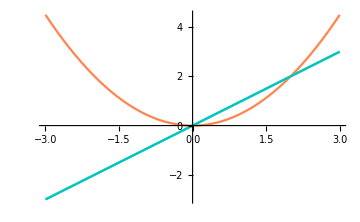
定义域 | 间断点
x∈ℝ | False
x∈ℝ | False
图像 | 
-Graphics- |

```mathematica
ClearAll[CorrectionTest];

CorrectionTest::overtime="`` 计算超时";

Options[CorrectionTest]:={Skip->{},TimeConstraint->∞,VerifyDiscontinuities->{},WorkingPrecision->$MinPrecision};
CorrectionTest[org_,res_,{x_,xmin_,xmax_},OptionsPattern[]]:=
Module[{
table={{Style["定义域",Bold], Style["间断点",Bold]}, {Style[True,Bold,RGBColor["#4081ff"]], Style[False,Bold,RGBColor["#4081ff"]]}, {Style[True,Bold,RGBColor["#eb7100"]], Style[False,Bold,RGBColor["#eb7100"]]}, {Style["图像",Bold], }, {Null, }},
skip=OptionValue[Skip],
cons=OptionValue[TimeConstraint],
veri=OptionValue[VerifyDiscontinuities],
prec=OptionValue[WorkingPrecision],
dom=True
},
CheckVersion[12.2];
If[!ListQ[skip],skip={skip}];
If[!ListQ[veri],veri={veri}];
If[!AssociationQ[cons],cons=Association["定义域"->cons,"间断点"->cons,"图像"->cons]];
If[!MemberQ[skip,"定义域"],
TimeConstrained[
table⟦2,1⟧=Item[Style[dom=Reduce[FunctionDomain[org,x],x∈Reals],Bold,RGBColor["#4081ff"]],ItemSize->Automatic];
table⟦3,1⟧=Item[Style[Reduce[FunctionDomain[res,x]&&dom,x∈Reals],Bold,RGBColor["#eb7100"]],ItemSize->Automatic];
,cons["定义域"],Message[CorrectionTest::overtime,"定义域"];
];
];
If[!MemberQ[skip,"间断点"],
TimeConstrained[
table⟦2,2⟧=Item[Style[Reduce[FunctionDiscontinuities[org,x]&&dom,x∈Reals],Bold,RGBColor["#4081ff"]],ItemSize->Automatic];
table⟦3,2⟧=Item[Style[Reduce[FunctionDiscontinuities[res,x]&&dom,x∈Reals],Bold,RGBColor["#eb7100"]],ItemSize->Automatic];
,cons["间断点"],Message[CorrectionTest::overtime,"间断点"];
];
];
If[!MemberQ[skip,"图像"],
TimeConstrained[
table⟦5,1⟧=Plot[
{org,res,Evaluate[D[(res/.{Abs[p_]->Piecewise[{{p, p>0}, {-p, p<0}}],Sign[p_]->Piecewise[{{1, p>0}, {-1, p<0}}]}), x]]},{x,xmin,xmax},
PlotStyle->96,ImageSize->Medium,
Epilog->{Black,PointSize[Medium],Point[
Block[{$MinPrecision=prec},N@Table[{i,res/.x->i},{i,veri}]]
]}
],cons["图像"],Message[CorrectionTest::overtime,"图像"];
];
];
Print[Grid[table,Alignment->{Center,Center},Spacings->{1,1},ItemSize->{Scaled[0.5],Automatic},Frame->All]];
];

CorrectionTest[x,x^2/2,{x,-3,3}]
```

## FindIdentities

```mathematica
ClearAll[FindIdentities];

FindIdentities[expr1_,expr2_,x_Symbol]/;RationalExpressionQ[expr1,x]&&RationalExpressionQ[expr2,x]:=
Module[{p1,p2,roots,limit},
p1=Numerator@Simplify@expr1 Denominator@Simplify@expr2;
p2=Numerator@Simplify@expr2 Denominator@Simplify@expr1;
roots=x/. Solve[D[p1/p2, x]==0,x];
If[!ListQ@roots,Return@{}];
DeleteDuplicates@Flatten@Reap[
Do[
limit=lim_(x->i) p1/p2//Simplify;
If[limit=!=0&&limit∈Rationals,
Sow[Defer@Evaluate@p1-limit p2==(p1-limit p2//Factor)]
];
,{i,roots}
]
][[2]]
];

FindIdentities[x^2-1,x+1,x]
FindIdentities[x^2+2x+5,(2x+3)^2,x]
FindIdentities[x^3-3 x^2-21x-25,(x+3)^3,x]
FindIdentities[4 x^3-9x+3,((x^2-3)/(x+1))^3,x]
```

{}

{-4/17 (3+2 x)^2+(5+2 x+x^2)==1/17 (-7+x)^2}

{(3+x)^3+(-25-21 x-3 x^2+x^3)==2 (1+x)^3}

{1/9 (-3+x^2)^3+(1+x)^3 (3-9 x+4 x^3)==1/9 x^2 (-135-180 x+18 x^2+108 x^3+37 x^4),-8/3 (-3+x^2)^3+(1+x)^3 (3-9 x+4 x^3)==1/3 (-15+9 x^2+2 x^3)^2}

## Li2Transform

```mathematica
ClearAll[Li2Transform];

Li2Transform[z_,f_Function]/;Module[{t,ft},ft=f@t//Together;PolynomialQ[ft,t]&&CoefficientList[ft,t]==={1,-1}]:=-PolyLog[2,1-z]-Log[z]Log[1-z]+π^2/6;
Li2Transform[z_,f_Function]/;Module[{t,ft},ft=f@t//Together;RationalExpressionQ[ft,t]&&CoefficientList[Denominator@ft,t]==={0,1}&&CoefficientList[Numerator@ft,t]==={1}]:=-PolyLog[2,1/z]-Log[-z] Log[z]+Log[z]^2/2+π^2/3;
Li2Transform[z_,f_Function]/;Module[{t,ft},ft=f@t//Together;RationalExpressionQ[ft,t]&&CoefficientList[Denominator@ft,t]==={0,1}&&CoefficientList[Numerator@ft,t]==={-1,1}]:=PolyLog[2,1-1/z]+Log[1-1/z] Log[1/z]-Log[-z] Log[z]+Log[z]^2/2+π^2/6;
Li2Transform[z_,f_Function]/;Module[{t,ft},ft=f@t//Together;RationalExpressionQ[ft,t]&&CoefficientList[Denominator@ft,t]==={1,-1}&&CoefficientList[Numerator@ft,t]==={1}]:=PolyLog[2,1/(1-z)]+1/2 Log[1-z]^2-Log[-z]Log[1-z]-π^2/6;
Li2Transform[z_,f_Function]/;Module[{t,ft},ft=f@t//Together;RationalExpressionQ[ft,t]&&CoefficientList[Denominator@ft,t]==={-1,1}&&CoefficientList[Numerator@ft,t]==={0,1}]:=-PolyLog[2,z/(-1+z)]+1/2 Log[1-z]^2-Log[1-z] Log[-z]-Log[1/(1-z)] Log[z/(-1+z)];
Li2Transform[z1_,z2_]/;PossibleZeroQ[z1+z2]:=1/2 PolyLog[2,z1^2];

ComplexPlot3D[{PolyLog[2,z]+PolyLog[2,-z]-Li2Transform[z,-z]},{z,-10-10I,10+10I}]
```

-Graphics3D-

## Ti2Transform

```mathematica
ClearAll[Ti2Transform];

Options[Ti2Transform]:={Defer->True};
Ti2Transform[z_,"倒数",OptionsPattern[]]:=
Module[{ti2=If[OptionValue[Defer],Defer,Identity]@Ti2},ti2[1/z]+Sign[z] π/2 Log@Abs[z]];
Ti2Transform[z_,a_,"倒数",OptionsPattern[]]:=
Module[{ti2=If[OptionValue[Defer],Defer,Identity]@Ti2},-ti2[1/z,1/a]+ti2[z]-ti2[a]+ArcTan[a]Log@Abs[a]-Sign[a] π/2 Log[(z √(a^2+1))/(z+a)]];
Ti2Transform[z_,a_,"交换",OptionsPattern[]]:=
Module[{ti2=If[OptionValue[Defer],Defer,Identity]@Ti2},ti2[a,z]+ti2[z]-ti2[a]+ArcTan[a]Log[(a √(z^2+1))/(z+a)]-ArcTan[z]Log[(z √(a^2+1))/(z+a)]];

Manipulate[Plot[{Ti2[z,a],Ti2Transform[z,a,"交换",Defer->False]},{z,-10,10}],{a,-10,10}]
```

## BivarablePlot

```mathematica
ClearAll[BivariablePlot];

Options[BivariablePlot]:={PlotLabels->None};
BivariablePlot[list_List,x_Symbol,OptionsPattern[]]:=
Module[{labels,isValid,const,constQ,edges,vertexes,usedVertexes,edgeStylize,vertexStylize},
labels=OptionValue@PlotLabels;
isValid=labels=!=None&&Length@list===Length@labels;
constQ[value_]:=FreeQ[value,x]&&!PossibleZeroQ@value;
edgeStylize[edge_,value_]:=Labeled[edge,Placed[Style[value,14,FontFamily->"CMU Serif"],.5]];
vertexStylize[value_]:=Framed[Style[value,Black,14,FontFamily->"CMU Serif"],FrameStyle->None];

edges=Table[
Piecewise[{{{bivars[[1]]<->bivars[[2]],const}, constQ[const=list[[bivars[[1]]]]^2+list[[bivars[[2]]]]^2//Simplify]}, {Piecewise[{{{bivars[[2]]->bivars[[1]],-const}, const<0//TrueQ}, {{bivars[[1]]->bivars[[2]],const}, True}}], constQ[const=list[[bivars[[1]]]]^2-list[[bivars[[2]]]]^2//Simplify]}, {Nothing, True}}]
,{bivars,Subsets[Range@Length@list,{2}]}];
usedVertexes=DeleteDuplicates@Cases[edges[[All,1]],_Integer,{2}];
vertexes=Table[i->(Evaluate@Inset[vertexStylize@Piecewise[{{labels[[i]]==list[[i]], isValid}, {list[[i]], True}}],#]&),{i,usedVertexes}];
edges=edgeStylize@@@edges;
Graph[edges,PlotTheme->"DiagramBlack",VertexLabels->None,VertexShapeFunction->vertexes,PlotRangePadding->Scaled@.1]
];

BivariablePlot[{x+√(1-x^2),x-√(1-x^2),√(2x √(1-x^2))},x]
BivariablePlot[{Cos[x]+Sin[x],Cos[x]-Sin[x],2Cos[x]+Sin[x],Cos[x]-2Sin[x]},x,PlotLabels->{p,q,m}]
BivariablePlot[{√x+a/(√x),√x-a/(√x),√(x+a^2/x+b),√(x+a^2/x+c)},x,PlotLabels->{p,q,r,s}]
```

-Graphics-

-Graphics-

-Graphics-